```mathematica
data =Import["D:\\学习\\大三下\\大物一级实验\\20170327 硅光电池特性研究\\作图.xlsx"]
```

{{{硅光电池暗伏安特性曲线（正向）,},{电压U/V,电流I/mA},{0.6106,1.},{0.7033,2.},{0.7551,3.},{0.8,4.},{0.8357,5.},{0.8634,6.},{0.8879,7.},{0.9102,8.},{0.9301,9.},{0.9492,10.},{0.9656,11.},{0.9834,12.},{0.9966,13.},{1.0121,14.},{1.0249,15.},{1.0403,16.},{1.0528,17.},{1.0661,18.},{1.0781,19.},{1.0906,20.}}}

```mathematica
data1 = data[[1]][[3;;]]
```

{{0.6106,1.},{0.7033,2.},{0.7551,3.},{0.8,4.},{0.8357,5.},{0.8634,6.},{0.8879,7.},{0.9102,8.},{0.9301,9.},{0.9492,10.},{0.9656,11.},{0.9834,12.},{0.9966,13.},{1.0121,14.},{1.0249,15.},{1.0403,16.},{1.0528,17.},{1.0661,18.},{1.0781,19.},{1.0906,20.}}

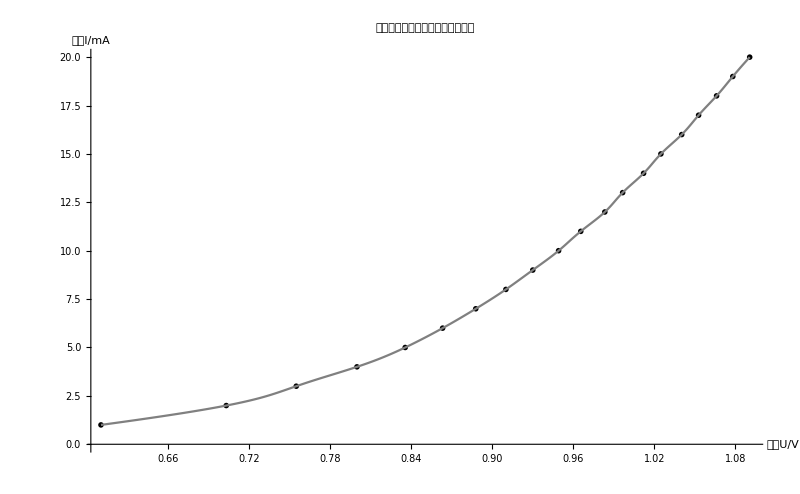

```mathematica
Show[
ListPlot[data1,PlotStyle->Black,PlotMarkers->{Style["X",10]}],
ListLinePlot[data1,PlotStyle->Gray, InterpolationOrder->4],
AxesLabel->{Style[data[[1]][[2]][[1]],15,Bold],Style[data[[1]][[2]][[2]],15,Bold]},
AxesStyle->Directive[Arrowheads[0.03],13],
PlotLabel->Style[data[[1]][[1]][[1]],18,FontFamily->"Adobe Fan Heiti Std",Bold],
ImageSize->{800,500}]
```

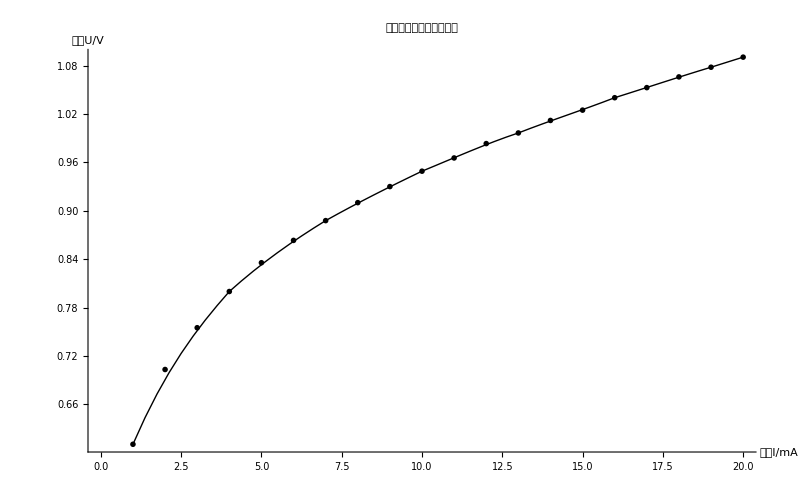

```mathematica
Show[
ListPlot[data1,PlotStyle->Black,PlotMarkers->{Style["X",10]}],
Graphics[BezierCurve[data1,SplineDegree->3]],
AxesLabel->{Style[data[[1]][[2]][[1]],15,Bold],Style[data[[1]][[2]][[2]],15,Bold]},
AxesStyle->Directive[Arrowheads[0.03],20],
PlotLabel->Style[data[[1]][[1]][[1]],18,FontFamily->"Adobe Fan Heiti Std",Bold],
ImageSize->{800,500}]
```